# Problema de los osciladores acoplados

## Diagrama del problema

```mathematica
Resorte[xMin_,xMax_,div_, yMin_ :0,yMax_ : 1]:=Block[{xValues,yValues,lineCoords},
xValues = Range[xMin,xMax,(xMax-xMin)/(div-1)];
yValues = PadRight[{yMin,yMax},Length[xValues],"Periodic"];
lineCoords = Transpose[{xValues,yValues}];
Line[lineCoords]
];
Masa[x_,label_,color_]:={EdgeForm[Thick],color,Rectangle[{x,0}],Black,Inset[Style[label,17],{x+0.5,0+0.5}]};
DiagramaOsciladores[x1_,x2_]:=Graphics[
{
Resorte[0,5+x1,10,0.2,0.8],
Resorte[5+x1,10+x2,10,0.2,0.8],
Resorte[10+x2,15,10,0.2,0.8],
Masa[5+x1,"m_1",RGBColor[1., 0, 0.11]],
Masa[10+x2,"m_2",RGBColor[0., 0.44, 0.55]],
{Thick,Line[{{0,0},{0,1}}]},
{Thick,Line[{{15,0},{15,1}}]}
},
ImageSize->500
];
```

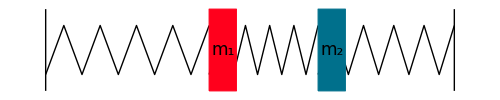

```mathematica
DiagramaOsciladores[1,0]
```

## Solución numerica

```mathematica
k = 1;
kP = 2;
{m1Solution,m2Solution} = NDSolveValue[
{
x1''[t]==-k x1[t] +kP (x2[t]-x1[t]),
x2''[t]==-k x2[t] +kP (x1[t]-x2[t]),
x1[0] ==1,x2[0]==0,
x1'[0] ==0,x2'[0]==0
},
{x1[t],x2[t]},{t,0,100}
]
```

{InterpolatingFunction[…][t],InterpolatingFunction[…][t]}

```mathematica
Manipulate[
DiagramaOsciladores[m1Solution/.t->tp,m2Solution/.t->tp],
{tp,0,100}
]
```

```mathematica
ExportImages[file_,frames_]:=Block[{indexLength,directory,name},
indexLength = Length[IntegerDigits[Length[frames]]];
directory = DirectoryName[file];
name = FileBaseName[file];

MapIndexed[
Export[
FileNameJoin[{directory,StringJoin[name,IntegerString[#2,10,indexLength],".png"]}],
#1
]&,
frames
]
];
```

```mathematica
Needs["AdvancedMapping`"];
```

```mathematica
imgs = ProgressTable[
DiagramaOsciladores[m1Solution/.t->tp,m2Solution/.t->tp],
{tp,0,10,0.01}
];
```

```mathematica
FileNameJoin[{NotebookDirectory[],"Animacion","imgs.png"}]
```

C:\Users\15-K212LA\Documents\Programacion\MetNum-UV\Unidad 3\Clase 13\Animacion\imgs.png

```mathematica
ExportImages[FileNameJoin[{NotebookDirectory[],"Animacion","imgs.png"}],imgs];
```

## Transformación lineal

```mathematica
PatternGrid[m_,n_]:=Map[
{{m.{-10,#},m.{10,#}},{m.{#,-10},m.{#,10}}}&,Range[-10,10,2/n]];
Lines[m_,n_]:=Map[Line,PatternGrid[m,n]];
```

```mathematica
DynamicModule[{m,lineas,eje,vector,etiquetas},
Manipulate[
m = Transpose[{i,j}];
lineas = Lines[m,5];
eje = {Thick,Blue,Arrow[{{0,0},m.{1,0}}],Thick,Red,Arrow[{{0,0},m.{0,1}}]};
etiquetas = {
Text[Panel[Style["î",14],FrameMargins->0],m.{0.5,0}],Text[Panel[Style["ĵ",14],FrameMargins->0],m.{0,0.5}],
Text[Panel[Style["OverVector[K . X]",14],FrameMargins->0],({{0.5, 0}, {0, 0.5}}).m.X]
};
vector = {Thick,Green,Arrow[{{0,0},m.X}]};
Column[
{
Row[{Style["Matriz K: ",Bold],MatrixForm[m],",    ",Style["X: ",Bold],MatrixForm[X]}],
Row[{Style["K.X: ",Bold],MatrixForm[m.X]}],
Style["Visualización",Bold],
Graphics[Join[lineas,eje,vector,etiquetas],PlotRange->{{-1.2,1.2},{-1.2,1.2}},ImageSize->300]
},
Left,
1
]
,
{{i,{1,0}},Locator},
{{j,{0,1}},Locator},
{{X,{0.7,0.7}},{-1,-1},{1,1}},
SaveDefinitions->True
]
]
```

## Visualización de osciladores como transformación lineal

```mathematica
DynamicModule[{m,v,lineas,eje,vector,etiquetas,original},
Manipulate[
m = -({{k+kP, -kP}, {-kP, k+kP}});
v = {m1Solution/.t->tp,m2Solution/.t->tp};
lineas = Lines[m,5];
eje = {Thick,Blue,Arrow[{{0,0},m.{1,0}}],Thick,Red,Arrow[{{0,0},m.{0,1}}]};
etiquetas = {
Text[Panel[Style["î",14],FrameMargins->0],m.{0.5,0}],Text[Panel[Style["ĵ",14],FrameMargins->0],m.{0,0.5}],
Text[Panel[Style["x⃗",14],FrameMargins->0],({{0.5, 0}, {0, 0.5}}).v],
Text[Panel[Style["m d^2/dt^2 x⃗",14],FrameMargins->0],({{0.5, 0}, {0, 0.5}}).m.v]
};
original = {Thick,Green,Arrow[{{0,0},v}]};
vector = {Thick,Yellow,Arrow[{{0,0},m.v}]};
Column[
{
Style["Matriz",Bold],
MatrixForm[m],
Style["Diagrama",Bold],
DiagramaOsciladores[m1Solution/.t->tp,m2Solution/.t->tp],
Style["Visualización",Bold],
Graphics[Join[lineas,eje,original,vector,etiquetas],PlotRange->{{-4,4},{-4,4}},ImageSize->500]
},
Left,
1
]
,
{tp,0,10},
SaveDefinitions->True
]
]
```

## Visualización de los eigenvectores

```mathematica
DynamicModule[{m,mEigenvectores,mEigenvalores,lineas,eje,vector,span,eigenvectores,etiquetas,eigenEtiquetas},
Manipulate[
m = Transpose[{i,j}];
mEigenvectores = Eigenvectors[m];
mEigenvalores = Eigenvalues[m];
lineas = Lines[m,5];
eje = {Thick,Blue,Arrow[{{0,0},m.{1,0}}],Thick,Red,Arrow[{{0,0},m.{0,1}}]};
span = {Thick,Orange,Arrow[{{0,0},v}]};
vector = {Thick,Green,Arrow[{{0,0},m.v}]};
etiquetas = {
Text[Panel[Style["î",12],FrameMargins->0],m.{0.5,0}],Text[Panel[Style["ĵ",12],FrameMargins->0],m.{0,0.5}],
Text[Panel[Style["span",12],FrameMargins->0],({{0.5, 0}, {0, 0.5}}).v],
Text[Panel[Style["v⃗",12],FrameMargins->0],({{0.5, 0}, {0, 0.5}}).m.v]
};


If[!MemberQ[mEigenvalores,_Complex],
eigenvectores = {
Dashed,Purple,Arrow[{{0,0},First[mEigenvectores]}],
Dashed,Brown,Arrow[{{0,0},Last[mEigenvectores]}]
};
eigenEtiquetas = {
Text[Panel[Style["OverVector[v_1]",12],FrameMargins->0],({{0.5, 0}, {0, 0.5}}).First[mEigenvectores]],
Text[Panel[Style["OverVector[v_2]",12],FrameMargins->0],({{0.5, 0}, {0, 0.5}}).m.Last[mEigenvectores]]
};
,
eigenvectores = {};
eigenEtiquetas ={};
];

Column[
{
Style["Matriz",Bold],
MatrixForm[m],
Style["Eigenvalores",Bold],
mEigenvalores,
Style["Eigenvectores",Bold],
Row[Map[Row,Transpose[{{"v_1 = ","v_2 = "},Map[MatrixForm,mEigenvectores]}]],", "],
Style["Visualización",Bold],
Graphics[Join[lineas,eje,vector,span,eigenvectores,etiquetas,eigenEtiquetas],PlotRange->{{-1.2,1.2},{-1.2,1.2}},ImageSize->300]
},
Left,
1
]
,
{{i,{1,0}},Locator},
{{j,{0,1}},Locator},
{{v,{0.7,0.7}},Locator},
SaveDefinitions->True
]
]
```

## Visualización de los eigenvectores de los osciladores

```mathematica
DynamicModule[{m,x,mEigenvectores,mEigenvalores,lineas,eje,vector,span,spanInTime,eigenvectores,etiquetas,eigenEtiquetas,m1Solution,m2Solution,k = 1,kP = 2},
Manipulate[
m = -({{k+kP, -kP}, {-kP, k+kP}});
{m1Solution,m2Solution} = NDSolveValue[
{
x1''[t]==-k x1[t] +kP (x2[t]-x1[t]),
x2''[t]==-k x2[t] +kP (x1[t]-x2[t]),
x1[0] ==x0[[1]],x2[0]==x0[[2]],
x1'[0] ==0,x2'[0]==0
},
{x1[t],x2[t]},{t,0,10}
];

x = {m1Solution/.t->tp,m2Solution/.t->tp};
mEigenvectores = Eigenvectors[m];
mEigenvalores = Eigenvalues[m];
lineas = Lines[m,5];
eje = {Thick,Blue,Arrow[{{0,0},m.{1,0}}],Thick,Red,Arrow[{{0,0},m.{0,1}}]};
span = {Thick,Orange,Arrow[{{0,0},x0}]};
spanInTime = {Thick,Yellow,Arrow[{{0,0},x}]};
vector = {Thick,Green,Arrow[{{0,0},m.x0}]};
etiquetas = {
Text[Panel[Style["î",12],FrameMargins->0],m.{0.5,0}],Text[Panel[Style["ĵ",12],FrameMargins->0],m.{0,0.5}],
Text[Panel[Style["x⃗",12],FrameMargins->0],({{0.5, 0}, {0, 0.5}}).x],
Text[Panel[Style["OverVector[x_0]",12],FrameMargins->0],({{0.5, 0}, {0, 0.5}}).x0],
Text[Panel[Style["m d^2/dt^2 x⃗",12],FrameMargins->0],({{0.5, 0}, {0, 0.5}}).m.x0]
};


If[!MemberQ[mEigenvalores,_Complex],
eigenvectores = {
Dashed,Purple,Arrow[{{0,0},First[mEigenvectores]}],
Dashed,Brown,Arrow[{{0,0},Last[mEigenvectores]}]
};
eigenEtiquetas = {
Text[Panel[Style["OverVector[v_1]",12],FrameMargins->0],({{0.5, 0}, {0, 0.5}}).First[mEigenvectores]],
Text[Panel[Style["OverVector[v_2]",12],FrameMargins->0],({{0.5, 0}, {0, 0.5}}).Last[mEigenvectores]]
};
,
eigenvectores = {};
eigenEtiquetas ={};
];

Column[
{
Style["Matriz",Bold],
MatrixForm[m],
Style["Eigenvalores",Bold],
mEigenvalores,
Style["Eigenvectores",Bold],
Row[Map[Row,Transpose[{{"v_1 = ","v_2 = "},Map[MatrixForm,mEigenvectores]}]],", "],
Style["Diagrama",Bold],
DiagramaOsciladores[x[[1]],x[[2]]],
Style["Visualización",Bold],
Graphics[Join[lineas,eje,vector,span,spanInTime,eigenvectores,etiquetas,eigenEtiquetas],PlotRange->{{-4,4},{-4,4}},ImageSize->500]
},
Left,
1
]
,
{{x0,{1,0}},Locator},
{tp,0,10},
SaveDefinitions->True
]
]
```